## AoC16 - Day 24

### Input

```mathematica
input="#######################################################################################################################################################################################
#.....................#.....#.#.......#.......#...#.....#.#...#.........#...........#...#.........#...#...#...#...#.........#.#.....#.........#.#.#.....#.....#.....#.#.#.............#
#.#.###.#.###.#.###.#.#.###.#.###.#########.#.#####.#####.#.###.#.#.#.#.###.#.###.#.#.#.#.###.#.#.#.#.###.#.#.#.#.###.#.#.#.#.#.#.#.#.###.#.#.#.#.#.#####.###.#.#.#.#.#.###.#.#.#.#.#.#
#.........#.......#...#.....#.#.#.#.......#.#.....#...#.....#.....#.....#...............#.#.#...#...#.#.....#.......#.#...#.....#.......#...#.#.#...#2#...#.................#...#.....#
#.###.#.###.#.#.#.#.#.#.#.#.#.#.#.#####.#.#.#.###.#.###.#.#.#.###.#.#.#.###.#.#.###.#.#####.#.#.#####.#.#.#.#######.#.#####.###.###.###.#.#.#.#.#.#.#.#.###.###.###.###.#.#.#.#.#######
#.#....1#.....#...#.......#...#.#.#.....#.....#.....................#.#...........#...#.....#.....#.....#.......#.....#.#.......#...........#...#.#...#...#...............#.#.#.#.....#
#.#.#######.#.#.#.#.#############.#.###.###.###.#.#.#########.#.###.#.#.#.#.#.#.#.#####.#.#.#.###.#.#.#.#.#.#.#.#.#.###.#########.#.#.#############.#######.#.#.#.###.###.###.#####.###
#.#.#...#.........#.....#.........#.....#.#.#...#...........#...#.........#...#.#.....#.#...............#...#.....#.#.#.............#.....#...#.....#...........#.#.#.....#...#.......#
#.###.#.#.#.#.#######.#.#.#.#.###.###.#.#.#.#.#.#.#.#####.###.#.#.#.#.#.#######.#.###.#.#.#.###.#.###.#.#.###.#.#.#.#.#.#.#.#.#.#######.#.###.#.###.#.###.#.#.###.#.###.#.#.#.#.#.#.###
#...#.#.........#.#...#.....#...#.......#.#.#.......#.#.#...#.........#.....#.#...#.#.#...#...#...#.....#.........#.#.....#.......#.....#.......#.#...#...#.....#.....#.......#.#.#...#
#.#.#.#.#.#.###.#.#.#.#.###.#####.#####.#######.#.###.#.#.#.#####.#.#####.###.#.#.#.#.#.#.###.#.#.#.#####.#.#####.#.###.#####.#.#.#.###.###.###.#.#.#.#####.#.#.#####.#.#######.#.#.###
#.....#.#.....#.........#.#...#.......#...#.......#.........#...#.#.#.#.......#...#...............#.#...................#.#.#.......#.#.........#....0#...#.#.......#.#.#.#...#.....#.#
#######.#.#.#.#######.###.#.###.#.#.#.#.#.#.#.#.###.###.#####.#.#.###.#.#.###.#####.#.#.#.#.#####.#.###.###.#.#.#######.#.#.#.#######.#.#.#.#.#.#.#.#.#.###.#.###.#.###.#.#####.#.#.#.#
#.........#...#...#.....#.........#.......#...#...........#.#.#.#...#...#.#...#.#...#.#.#.......#.......#...#.....#.....#.#...#.#.#.#.........#...............#...#.#...........#.....#
#.#.#.#.#.#####.###.#####.#.#######.#.#.#.#.#.#.#.#####.###.#.#.#.#.#.###.#.#.#.#.#.#.#.#.#.#.#.###.#.###.#.###.#.#.#.#.#.###.#.#.#.#.#.#.#.#.#.#####.###.###.#.#######.#.###.#.#######
#.#...#...#...#.....#.#.#.#...#.................#...#...#.#...#...#...#.#.#.#.....#.#.#.....#.#...#.#.......#.#.#...#...#.#...#.....#...#.#...#...#.....#.....#...#.....#.....#.#...#.#
#.###.###.###.###.#.#.#.#.#.#.#.#.#.###.#.###.#####.#.###.#.###.###.#.#.#.#.#.###.#.###.#####.###.###.#.#.#.#.#.#.#.#.#.#.#.###.#.#.#.###.#####.#.###########.#.#.#.###.#.#######.#.#.#
#..3#.#.......#...#.............#.....#.....#...#...#.#.....#.......#.....#...#.....#.#.#.........#...#.#.........#.....#...............#.........#...#...........#.#.#...#7#.#.....#.#
###.#.#.###.#.#.###.#############.###.#.#######.#.#####.#######.#####.#.###.#.#.#.#.#.#.#.#.#.#.#.###.#.#########.#.#.#.#.#.#.###.#.###.#####.#####.###.#.###.#.#.#.#.#.#.#.#.#.###.#.#
#.#...#.....#.#.#.#.#.#...........................#.......#...#.#.....#.#...#...#.#...#.........#...........#.#.....#.....#...#...#.#.......#.#.#...#...#.#.......#.......#...#.....#.#
#.#########.#.#.#.#.#.#.#.#####.###.#######.#.#####.#.#.#.#.###.#.#.#.#.#####.#######.#.#####.#.#.#.#####.#.#.#.###.#####.#.#######.#######.###.###.#.#.#.###.###.#.#########.#.#.###.#
#.#.......#...#.....#.#.......#.#...#.....#...........#.#...........#...#.....#.........#.......#...#.........#.#.....#.#...#.............#.............#...........#.....#...#.#.#.#.#
#.#.###.#.#.#.#.#.###.###.#####.#.#.#.#.#.###.#.#####.#.#.#.#.###.#####.#######.#.#.#.#.#.#.#.#.#.#.###.#.###.#.#.#.#.#.#.###.#.###.#.###.#######.###.#.#.#.#.###.###.#.#.#.#.#.#.#.###
#.#.......................#.......#.......#.#.#.......#...........#...#...#.....#.#.#...#...#...#.......#.......#.#.#...#.....#.....#...#...#.....#.#...#...#...........#.....#...#...#
#.#.###.#####.#.###.#.#.###.#.#.#.#######.#.#####.#.#.###.#.#######.#.#.#.#.#.#.###.#.#.#.#.#.#.#.###.#.###.#.###.###.#######.#.###.###.#.#.#.###.#.###.###.###.#.#.#.#.#.#.#.#.###.#.#
#...#.....#.........#...#.#.....#...#...#.#.#...#.....#.#.#...#.......#.....#.......#.....#.....#.#.....#...#.#.#.......#...#.#...#.........#...#...........#...#...#...#.....#.#.#.#.#
#########.###.#####.#.#.#.#.#.###.#.#.###.#.#.#.#.###.#.#.#.#.#.#.###.#.###.#.#####.#######.#.###.#.###.#.#.###.#.#.#####.#######.#.###.#.###.###.#.###.#.#.#.###.#.#######.#.###.#.#.#
#.#...#...#...#.....#...#.#6......#.#.....#.....#.....#.#...#...#...#.#.....#...#...#...#...#.............#.#...#.......#.#...#...........#.#..5#...#.#.....#...#.....#...#...#.......#
#.###.#.#.###.###.#.#.#.#.#####.#.#.#####.#.#.###.#.#.#.#.#.#.###.#.#.###.#.#########.###.###.#######.#.#.#.#.#.#.#####.#.#.#.#.#.###.#.###.#####.#.#.#.#.#.#.#.###.#.###.#.###.#.#.#.#
#.#...#...#...#.........#...#.................#.....#.....#...............#.....#.#...#.....#.......#...#.....#.#.#.......#.............#.#.#.#...#.#...#.#.#...#.....#.......#.......#
#.###.#.###.###.###.#.#.#.#.#.###.###.#.#.###.###.###############.#####.#.#######.#.#.#.###########.###.#.#.#.#.#.#.#.###.#.#####.#######.###.#.#.#.#.###.#.#.#.#.###.###.###.#.#.###.#
#...................#...........#.#.#.........#.....#...#...#...#.#.....#.........#...#.#.......#...#...............#.#.................#.....#.....#.#.....#...#...#.#.....#...#.....#
#.#.#.#.#.###.###.#.###.#.#####.#.#.#########.#.#.###.#.###.#####.#.#.#.#.#.#.#######.#####.#.#.#.###.#.#.###.#####.#.#.#.###.###.###.###.#######.#.#.#.###.#.#.#.#.#.#.#.###.#.#.###.#
#.#...#.#.#.#.......#.#...#.#.....#.......#.#.#.....#.#.#.......#...#.#.....#.#...#...#.........#.......#.....#.#...#...#.......#.#...#...#.#.........#...#.........#.........#.#.#...#
###.#####.#.#.###.#.#.#.###.#.#.#.#.#.#.#.#.#.#####.###.#.###.#.#.#.#.#.#.#.#######.#.###.#.#####.###.#####.###.#.#.###.#.#.#.###.#.###.#.#.#.#.#####.#.#####.###.#.#.#.###.#####.#.#.#
#...........#...................#.....#.....#...............#...#.#.....#.......#...#...#...#...#.......#...#...#.....#...#...#...#.....#4#...#...#...#.....#.............#.#...#.....#
#######################################################################################################################################################################################";
```

### Part 1

```mathematica
rows=StringSplit[StringReplace[input,{"1"->"*","2"->"*","3"->"*","4"->"*","5"->"*","6"->"*","7"->"*","8"->"*","9"->"*"}],"\n"];
```

```mathematica
chars=Characters/@rows;
```

```mathematica
Image[chars/.{"#"->0,"*"->1,"."->1,"0"->0.5},ImageSize->800]
```

-Graphics-

```mathematica
CreateGraph[data_]:=Module[{H,W,x,y,g,targets,start},
H=Length@data;
W=Length@data[[1]];
g={};
targets={};
start=0;
For[x=1,x≤W-1,x++,
For[y=1,y≤H-1,y++,
If[(data⟦y,x⟧!="#"),
If[(data⟦y+1,x⟧!="#"),AppendTo[g,{y,x}<->{y+1,x}]];
If[(data⟦y,x+1⟧!="#"),AppendTo[g,{y,x}<->{y,x+1}]];
];
If[(data⟦y,x⟧=="*"),AppendTo[targets,{y,x}]];
If[(data⟦y,x⟧=="0"),start={y,x}];
];
];
{g,targets,start}
]
```

```mathematica
{g,t,s}=CreateGraph[chars];
```

Start:

```mathematica
s
```

{12,150}

Targets:

```mathematica
t
```

{{18,4},{6,8},{28,28},{36,138},{28,144},{4,150},{18,172}}

```mathematica
locations={s}~Join~t
```

{{12,150},{18,4},{6,8},{28,28},{36,138},{28,144},{4,150},{18,172}}

```mathematica
shortestPaths=Table[Length@FindShortestPath[g,locations[[i]],locations[[j]]]-1,{i,1,Length@locations},{j,1,Length@locations}];
```

```mathematica
shortestPaths//Grid
```

0 | 208 | 200 | 174 | 64 | 42 | 12 | 48
208 | 0 | 40 | 62 | 204 | 214 | 208 | 252
200 | 40 | 0 | 66 | 204 | 206 | 200 | 244
174 | 62 | 66 | 0 | 166 | 180 | 174 | 218
64 | 204 | 204 | 166 | 0 | 66 | 68 | 104
42 | 214 | 206 | 180 | 66 | 0 | 54 | 58
12 | 208 | 200 | 174 | 68 | 54 | 0 | 60
48 | 252 | 244 | 218 | 104 | 58 | 60 | 0

```mathematica
st[[1]]-42
```

546

#### All collectable locations

```mathematica
weightedData2=Flatten[Table[{i<->j,shortestPaths[[j,i]]},{j,2,Length@locations},{i,j+1,Length@locations}],1]
edges2=weightedData2⟦All,1⟧
edgeWeights2=weightedData2⟦All,2⟧
```

{{3<->2,40},{4<->2,62},{5<->2,204},{6<->2,214},{7<->2,208},{8<->2,252},{4<->3,66},{5<->3,204},{6<->3,206},{7<->3,200},{8<->3,244},{5<->4,166},{6<->4,180},{7<->4,174},{8<->4,218},{6<->5,66},{7<->5,68},{8<->5,104},{7<->6,54},{8<->6,58},{8<->7,60}}

{3<->2,4<->2,5<->2,6<->2,7<->2,8<->2,4<->3,5<->3,6<->3,7<->3,8<->3,5<->4,6<->4,7<->4,8<->4,6<->5,7<->5,8<->5,7<->6,8<->6,8<->7}

{40,62,204,214,208,252,66,204,206,200,244,166,180,174,218,66,68,104,54,58,60}

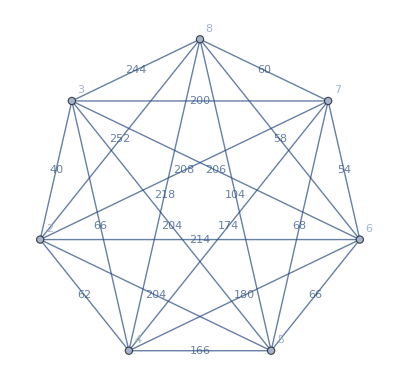

```mathematica
wg2=Graph[edges2,EdgeWeight->edgeWeights2,VertexLabels->Automatic,EdgeLabels->Thread[edges2->edgeWeights2]]
```

{652,{3,7,8,6,5,4,2,3}}

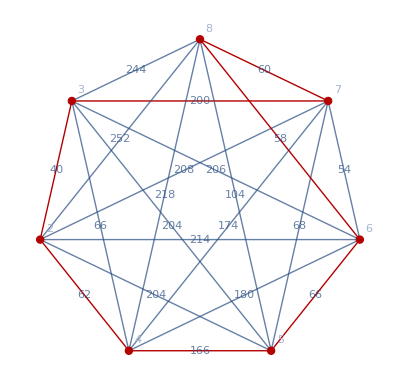

464

```mathematica
st2=FindShortestTour[wg2]
HighlightGraph[wg2,PathGraph[st2⟦2⟧]]
st2⟦1⟧-200+12
```

```mathematica
Flatten[Table[{i<->j,shortestPaths[[j,i]]},{j,1,1},{i,j+1,Length@locations}],1]
```

{{2<->1,208},{3<->1,200},{4<->1,174},{5<->1,64},{6<->1,42},{7<->1,12},{8<->1,48}}

#### Answer: 464, correct

### Part 2:

```mathematica
weightedData=Flatten[Table[{i<->j,shortestPaths[[j,i]]},{j,1,Length@locations},{i,j+1,Length@locations}],1];
edges=weightedData⟦All,1⟧;
edgeWeights=weightedData⟦All,2⟧;
```

```mathematica
wg=Graph[edges,EdgeWeight->edgeWeights,VertexLabels->Automatic,EdgeLabels->Thread[edges->edgeWeights]];
```

```mathematica
st=FindShortestTour[wg]
```

{652,{2,3,7,1,8,6,5,4,2}}

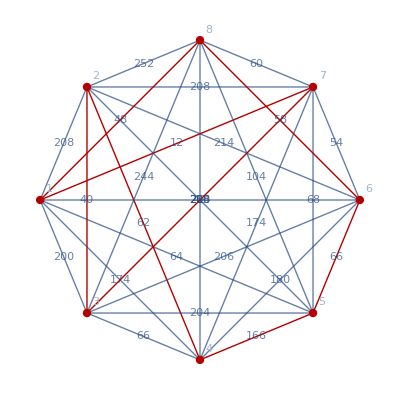

```mathematica
HighlightGraph[wg,PathGraph[st[[2]]]]
```